```mathematica
dir=NotebookDirectory[]
SetDirectory[dir];
```

/Users/stefanhallermann/Desktop/github/parallel/out/

## traces

File number: 1

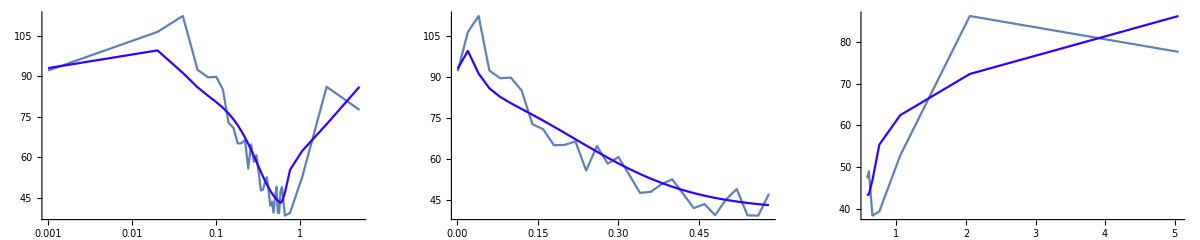

File number: 2

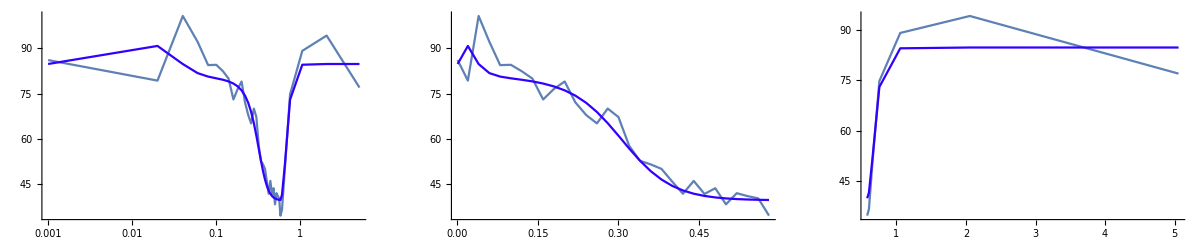

File number: 3

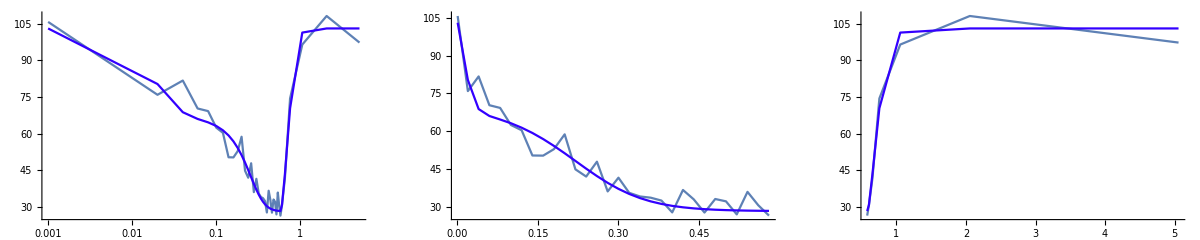

File number: 4

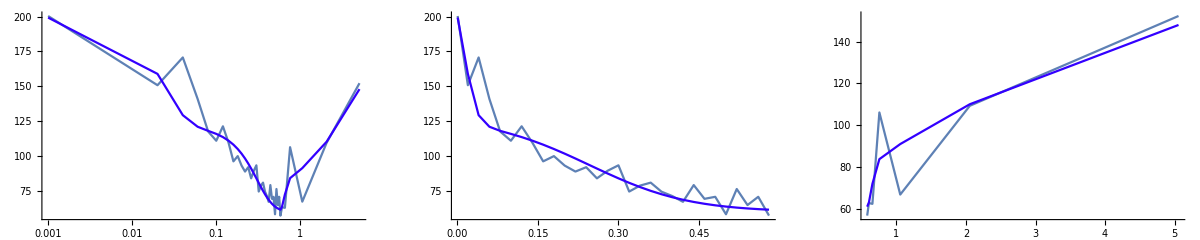

File number: 5

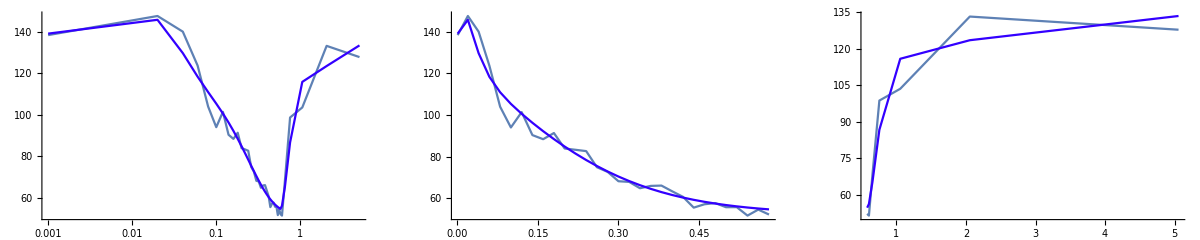

File number: 6

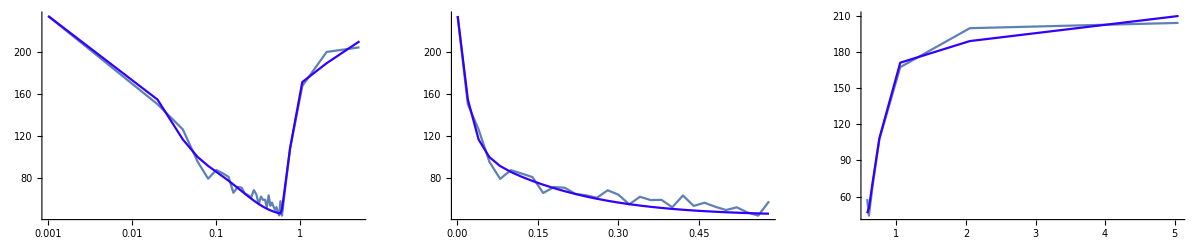

```mathematica
time300=Flatten[Import["time300.txt","Table"]];
time300[[1]]+=0.001;
tmp300=Import["apAmp300.txt","Table"];
tmpSim300=Import["apAmp300Sim.txt","Table"];
numFiles=Length[tmp300[[1,All]]];

t300t1=25;
t300t2=34;
train=30;
plR={All,All};

For[i=1,i≤numFiles,i+=1,
amp300=tmp300[[All,i]];
ampSim300=tmpSim300[[All,i]];
Print["File number: ",i];
(*log*)
tmp1=ListLogLinearPlot[Transpose[{time300,amp300}],PlotRange->All,Joined->True,DisplayFunction -> Identity];
tmp2=ListLogLinearPlot[Transpose[{time300,ampSim300}],PlotRange->All,Joined->True,PlotStyle->Hue[0.7],DisplayFunction -> Identity];
gr300=Show[{tmp1,tmp2},PlotRange->plR,DisplayFunction -> Identity];
(*train*)
tmp1=ListPlot[Take[Transpose[{time300,amp300}],train],PlotRange->All,Joined->True,DisplayFunction -> Identity];
tmp2=ListPlot[Take[Transpose[{time300,ampSim300}],train],PlotRange->All,Joined->True,PlotStyle->Hue[0.7],DisplayFunction -> Identity];
gr300tr=Show[{tmp1,tmp2},PlotRange->plR,DisplayFunction -> Identity];
(*recovery after train*)
tmp1=ListPlot[Take[Transpose[{time300,amp300}],{train,Length[time300]}],PlotRange->All,Joined->True,DisplayFunction -> Identity];
tmp2=ListPlot[Take[Transpose[{time300,ampSim300}],{train,Length[time300]}],PlotRange->All,Joined->True,PlotStyle->Hue[0.7],DisplayFunction -> Identity];
gr300rec=Show[{tmp1,tmp2},PlotRange->plR,DisplayFunction -> Identity];
Print[GraphicsGrid[{{gr300,gr300tr,gr300rec}}]];
];
```

## rates and chi2

```mathematica
tmp=Import["rates.txt","Table"];
Flatten[{{{"n2tot","n1tot","U2","k2","k1","chi2_train"}},tmp},1]//MatrixForm
```

(n2tot | n1tot | U2 | k2 | k1 | chi2_train
4.93945 | 15.9518 | 0.474224 | 0.465751 | 81.7833 | 15.0561
7.59598 | 9.88013 | 0.444882 | 16.5356 | 547.541 | 8.1691
6.57494 | 6.60393 | 0.686753 | 13.131 | 211.527 | 4.70488
12.0778 | 17.0381 | 0.636626 | 0.244394 | 135.691 | 31.0516
3.00388 | 27.1286 | 0.552543 | 0.438664 | 30.3038 | 7.96377
4.18736 | 24.3987 | 0.938826 | 0.304159 | 19.9093 | 8.10589)